```mathematica
(*ONE-DIMENSIONAL CASE*)
```

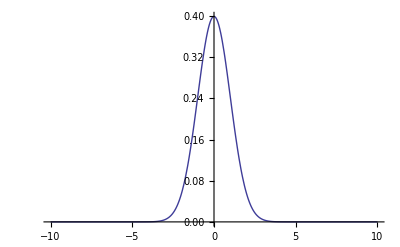

```mathematica
px[x_]:=PDF[NormalDistribution[0,1],x]
Plot[px[x],{x,-10,10}, PlotRange->All]
```

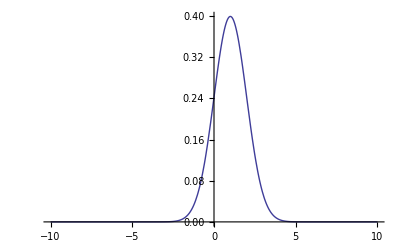

```mathematica
py[y_]:=PDF[NormalDistribution[1,1],y]
Plot[py[y],{y,-10,10}, PlotRange->All]
```

```mathematica
pm[dx_]:=NIntegrate[px[x]py[x-dx],{x,-10,10}]
(*Plot[pm[dx],{dx,-10,10}, PlotRange->All]*)
```

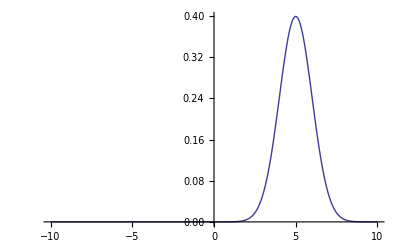

```mathematica
pz[z_]:=PDF[NormalDistribution[5,1],z]
Plot[pz[z],{z,-10,10},PlotRange->All]
```

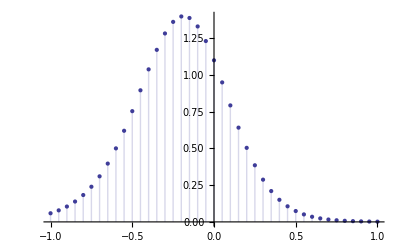

```mathematica
Clear[pd]
pd[n_]:=NIntegrate[pm[n*z]pz[z]z, {z,-10,10},MinRecursion->2,MaxRecursion->3];
x=Array[pd,41,{-1,1}];
n=Range[-1,1,0.05];
ListPlot[Thread[{n,x}],Filling->Axis]
(*ListPlot[Thread[{dz,pd}], Filling-> Axis]*)
(*NIntegrate gives an error when the integrand contains a parameter that does not have a numerical value, which in our case is dz. One way to get round the problem is to define an array for dz, and then evaluate pd[dz_] at each of those values, and then plot it*)
```

```mathematica
(*TWO-DIMENSIONAL CASE*)
```

```mathematica
Clear[px1x2,py1y2,pz1z2,x1,x2,y1,y2,z1,z2]
px1x2[x1_,x2_]:=PDF[MultinormalDistribution[{0,0},{{1,0},{0,1}}],{x1,x2}]
py1y2[y1_,y2_]:=PDF[MultinormalDistribution[{1,1},{{1,0},{0,1}}],{y1,y2}]
pz1z2[z1_,z2_]:=PDF[MultinormalDistribution[{2,2},{{1,0},{0,1}}],{z1,z2}]
Plot3D[px1x2[x1,x2],{x1,-2,2},{x2,-2,2}, PlotRange->All]
Plot3D[py1y2[y1,y2],{y1,-1,3},{y2,-1,3}, PlotRange->All]
Plot3D[pz1z2[z1,z2],{z1,0,4},{z2,0,4}, PlotRange->All]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
Clear[pm2d,x1,x2,dx1,dx2]
pm2d[dx1_,dx2_]:=Integrate[f[x1,x2]g[x1-dx1,x2-dx2],{x1,-10,10},{x2,-10,10}]
(*Plot3D[pm2d[dx1,dx2],{dx1,-7,3},{dx2,-7,3},PlotRange->All]*)
```

```mathematica
Clear[pd2dintegrant,pd2dintegral,dz1,dz2,x]
(*pd2dintegrant[dz1_,dz2_,z1_,z2_]:=pm2d[dz1*z1,dz2*z2]pz1z2[z1,z2]z1*z2*)
pd2dintegral[dz1_,dz2_]:=NIntegrate[pm2d[dz1*z1,dz2*z2]pz1z2[z1,z2]z1*z2,{z1,-100,100},{z2,-10,10},MinRecursion->5]
dz1=Range[-1.5,0.5,0.2];
dz2=Range[-1.5,0.5,0.2];
(*Plot3D[pd2dintegrant[0.1,0.1,z1,z2],{z1,-100,100},{z2,-10,10},PlotRange->All]*)
x=Array[pd2dintegral,{11,11},{{-2,1},{-2,1}}];
ListPlot3D[x,MeshStyle->Opacity[0.4],InterpolationOrder->3,ColorFunction->"SouthwestColors",DataRange->{{-1,1},{-1,1},Automatic}]
```

NIntegrate::inumr: The integrand ⅇ^1/2\ (-(-2 + z1)^2 - (-2 + z2)^2)\ z1\ z2\ ∫_-10 10 ∫_-10 10 f[x1, x2]\ g[x1 + 2\ z1, x2 + 2\ z2] ⅆ x2 ⅆ x1/2\ π has evaluated to non-numerical values for all sampling points in the region with boundaries {{-100., -93.75}, {-10., -9.375}}.

NIntegrate::inumr: The integrand ⅇ^1/2\ (-(-2 + z1)^2 - (-2 + z2)^2)\ z1\ z2\ ∫_-10 10 ∫_-10 10 f[x1, x2]\ g[x1 + 2\ z1, x2 + 17\ z2/10] ⅆ x2 ⅆ x1/2\ π has evaluated to non-numerical values for all sampling points in the region with boundaries {{-100., -93.75}, {-10., -9.375}}.

NIntegrate::inumr: The integrand ⅇ^1/2\ (-(-2 + z1)^2 - (-2 + z2)^2)\ z1\ z2\ ∫_-10 10 ∫_-10 10 f[x1, x2]\ g[x1 + 2\ z1, x2 + 7\ z2/5] ⅆ x2 ⅆ x1/2\ π has evaluated to non-numerical values for all sampling points in the region with boundaries {{-100., -93.75}, {-10., -9.375}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

```mathematica
(*OUR CASE*)
```

```mathematica
Clear[px1x2,py1y2,pz1z2,x1,x2,y1,y2,z1,z2]
px1x2[x1_,x2_]:=PDF[MultinormalDistribution[{100,0.5},{{10,0},{0,0.1}}],{x1,x2}]
py1y2[y1_,y2_]:=PDF[MultinormalDistribution[{100,0.5},{{50,0},{0,0.5}}],{y1,y2}]
pz1z2[z1_,z2_]:=PDF[MultinormalDistribution[{100,0.5},{{5,0},{0,0.05}}],{z1,z2}]
Plot3D[px1x2[x1,x2],{x1,80,120},{x2,-0.5,1.5}, PlotRange->All]
Plot3D[py1y2[y1,y2],{y1,80,120},{y2,-0.5,1.5}, PlotRange->All]
Plot3D[pz1z2[z1,z2],{z1,80,120},{z2,-0.5,1.5}, PlotRange->All]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
Clear[pm2d,x1,x2,dx1,dx2]
pm2d[dx1_,dx2_]:=Integrate[f[x1,x2]g[x1-dx1,x2-dx2],{x1,-500,500},{x2,-5,5}]
Plot3D[pm2d[dx1,dx2],{dx1,-10,5},{dx2,-5,5},PlotRange->All]
```

NIntegrate::inumr: The integrand f[x1, x2]\ g[9.99893  + x1, 4.99929  + x2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-500, 500}, {-5, 5}}.

NIntegrate::inumr: The integrand f[x1, x2]\ g[9.99893  + x1, 4.99929  + x2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-500., 500.}, {-5., 5.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

-Graphics3D-

```mathematica
Clear[pd2dintegrant,pd2dintegral,dz1,dz2,x]
(*pd2dintegrant[dz1_,dz2_,z1_,z2_]:=pm2d[dz1*z1,dz2*z2]pz1z2[z1,z2]z1*z2*)
pd2dintegral[dz1_,dz2_]:=NIntegrate[pm2d[dz1*z1,dz2*z2]pz1z2[z1,z2]z1*z2,{z1,-500,500},{z2,-5,5},MinRecursion->5]
dz1=Range[-10,10,0.5];
dz2=Range[-5,5,0.5];
(*Plot3D[pd2dintegrant[0.1,0.1,z1,z2],{z1,-100,100},{z2,-10,10},PlotRange->All]*)
x=Array[pd2dintegral,{21,21},{{-10,10},{-10,10}}];
ListPlot3D[x,MeshStyle->Opacity[0.4],InterpolationOrder->3,ColorFunction->"SouthwestColors",DataRange->{{-10,10},{-10,10},Automatic},AxesLabel->{"v1","v2","P_v1v2"},PlotRange->All]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.8319302094662208006904672601287845919672852284598571982067050735×10^-319 and 5.8073034498221677840466261996702977544643908322245399718974142439×10^-322 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.5716225283875943386709904966188246750659829926433898134198308911×10^-318 and 2.1613762276495131396951669657640246833657153649243107779032618223×10^-322 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.7494498468899472213557767444729551184859581709922149037964603224×10^-318 and 9.0784387166564481320299707178405078378610590281212034182346518988×10^-322 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

-Graphics3D-